### Smoothed analysis for trajectories

#### Yellow flowers

```mathematica
(*this is from main notebook*)
```

```mathematica
ydists=Flatten[yellowdistspeeds,1][[All,1]];
yspeeds=Flatten[yellowdistspeeds,1][[All,2]];
```

Controls

```mathematica
(*this is from control notebook*)
```

```mathematica
ycdists=Flatten[yellowcontrolspeeds,1][[All,1]];
ycspeeds = Flatten[yellowcontrolspeeds,1][[All,2]];
```

#### White flowers

```mathematica
(*this is from main notebook*)
```

```mathematica
wdists=Flatten[whitedistspeeds,1][[All,1]];
wspeeds=Flatten[whitedistspeeds,1][[All,2]];
```

Controls

```mathematica
(*this is from control notebook*)
```

```mathematica
ycdists=Flatten[yellowcontrolspeeds,1][[All,1]];
ycspeeds = Flatten[yellowcontrolspeeds,1][[All,2]];
```

```mathematica
wcdists=Flatten[whitecontrolspeeds,1][[All,1]];
wcspeeds = Flatten[whitecontrolspeeds,1][[All,2]];
```

#### Function to smooth

```mathematica
MovingAverageFunction[Dists_,Speeds_]:=Module[{windowSize,smoothedDistances,smoothedSpeeds},
windowSize=5;
smoothedDistances=MovingAverage[Dists,windowSize];
smoothedSpeeds=MovingAverage[Speeds,windowSize];
Return[{smoothedDistances,smoothedSpeeds}ᵀ]
]
```

#### Smoothed data

```mathematica
YdistSpeed=MovingAverageFunction[ydists,yspeeds];
```

```mathematica
YCdistSpeed=MovingAverageFunction[ycdists,ycspeeds];
```

```mathematica
WdistSpeed=MovingAverageFunction[wdists,wspeeds];
```

```mathematica
WCdistSpeed=MovingAverageFunction[wcdists,wcspeeds];
```

#### Plot

```mathematica
ListFitPlot[{YCdistSpeed,YdistSpeed, WCdistSpeed,WdistSpeed},PlotFit->"Linear", PlotRange->{{0,30},{0,300}}, PlotStyle->{StandardOrange,{Dashed,StandardOrange}, Blue, {Dashed,StandardBlue}},PlotFitElements->"None"]
```

-Graphics-

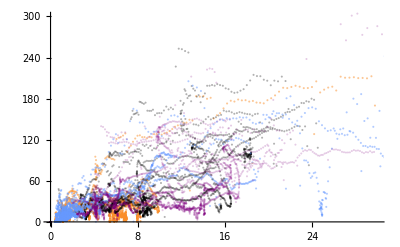

```mathematica
ListPlot[{YCdistSpeed,YdistSpeed, WCdistSpeed,WdistSpeed},
 PlotRange->{{0,30},{0,300}},
 PlotStyle->{Opacity[0.5,StandardOrange],Opacity[0.3,Black],Opacity[0.5,StandardBlue],Opacity[0.2,Purple]}]
```

```mathematica
Show[,,Frame->True,FrameLabel->{{"Speed (cm/s)",None},{"Distance to flower (cm)",None}},FrameTicks->{{All,None},{All,None}},FrameStyle->GrayLevel[0]]
```

-Graphics-

```mathematica
Export["speeddists.pdf",%92]
```

speeddists.pdf

### Difference in slopes

```mathematica
wmodel=LinearModelFit[WdistSpeed,x,x];
ymodel =LinearModelFit[YdistSpeed,x,x];
```

```mathematica
wcmodel=LinearModelFit[WCdistSpeed,x,x];
ycmodel =LinearModelFit[YCdistSpeed,x,x];
```

#### Test for differences in slope between treatments and controls

yellow

```mathematica
model1 =ymodel;
model2 =ycmodel;

(* Extract parameter information including slopes *)
(* Get the slope coefficients and their standard errors *)
slope1 = model1["BestFitParameters"][[2]];
slope2 = model2["BestFitParameters"][[2]];
stderr1 = model1["ParameterErrors"][[2]];
stderr2 = model2["ParameterErrors"][[2]];

(* Calculate the difference between slopes *)
slopeDiff = slope1 - slope2;

(* Calculate standard error of the difference *)
seDiff = Sqrt[stderr1^2 + stderr2^2];

(* Calculate t-statistic *)
tStat = slopeDiff/seDiff;

(* Extract degrees of freedom from ANOVA tables correctly *)
anovaTable1 = model1["ANOVATable"];
anovaTable2 = model2["ANOVATable"];

(* Find the Error row in each ANOVA table *)
df1 = Cases[anovaTable1, {"Error", df_, ___} :> df, Infinity][[1]];
df2 = Cases[anovaTable2, {"Error", df_, ___} :> df, Infinity][[1]];


(* Use the pooled degrees of freedom *)
df = df1 + df2;

(* Calculate p-value (two-tailed test) *)
pValue = 2 * (1 - CDF[StudentTDistribution[df], Abs[tStat]]);

(* Print results *)
Print["Slope 1: ", slope1, " ± ", stderr1];
Print["Slope 2: ", slope2, " ± ", stderr2];
Print["Difference: ", slopeDiff, " ± ", seDiff];
Print["t-statistic: ", tStat];
Print["Degrees of freedom: ", df];
Print["p-value: ", pValue];
Print["Significant difference at α=0.05: ", pValue < 0.05]
```

General::munfl: Exp[-752.273] is too small to represent as a normalized machine number; precision may be lost.

Slope 1: 5.83697 ± 0.147782

Slope 2: 5.5672 ± 0.123121

Difference: 0.269769 ± 0.19235

t-statistic: 1.40249

Degrees of freedom: 4957

p-value: 0.160831

Significant difference at α=0.05: False

white

```mathematica
model1 =wmodel;
model2 =wcmodel;

(* Extract parameter information including slopes *)
(* Get the slope coefficients and their standard errors *)
slope1 = model1["BestFitParameters"][[2]];
slope2 = model2["BestFitParameters"][[2]];
stderr1 = model1["ParameterErrors"][[2]];
stderr2 = model2["ParameterErrors"][[2]];

(* Calculate the difference between slopes *)
slopeDiff = slope1 - slope2;

(* Calculate standard error of the difference *)
seDiff = Sqrt[stderr1^2 + stderr2^2];

(* Calculate t-statistic *)
tStat = slopeDiff/seDiff;

(* Extract degrees of freedom from ANOVA tables correctly *)
anovaTable1 = model1["ANOVATable"];
anovaTable2 = model2["ANOVATable"];

(* Find the Error row in each ANOVA table *)
df1 = Cases[anovaTable1, {"Error", df_, ___} :> df, Infinity][[1]];
df2 = Cases[anovaTable2, {"Error", df_, ___} :> df, Infinity][[1]];


(* Use the pooled degrees of freedom *)
df = df1 + df2;

(* Calculate p-value (two-tailed test) *)
pValue = 2 * (1 - CDF[StudentTDistribution[df], Abs[tStat]]);

(* Print results *)
Print["Slope 1: ", slope1, " ± ", stderr1];
Print["Slope 2: ", slope2, " ± ", stderr2];
Print["Difference: ", slopeDiff, " ± ", seDiff];
Print["t-statistic: ", tStat];
Print["Degrees of freedom: ", df];
Print["p-value: ", pValue];
Print["Significant difference at α=0.05: ", pValue < 0.05]
```

General::munfl: Exp[-1064.36] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-822.742] is too small to represent as a normalized machine number; precision may be lost.

Slope 1: 6.97139 ± 0.123872

Slope 2: 3.18743 ± 0.0646211

Difference: 3.78396 ± 0.139714

t-statistic: 27.0836

Degrees of freedom: 5008

p-value: 0.

Significant difference at α=0.05: True

#### Test for differences in slope between white and yellow flowers

```mathematica
(* Extract parameter information including slopes *)
(* Get the slope coefficients and their standard errors *)
slope1 = ymodel["BestFitParameters"][[2]];
slope2 = wmodel["BestFitParameters"][[2]];
stderr1 = ymodel["ParameterErrors"][[2]];
stderr2 = wmodel["ParameterErrors"][[2]];

(* Calculate the difference between slopes *)
slopeDiff = slope1 - slope2;

(* Calculate standard error of the difference *)
seDiff = Sqrt[stderr1^2 + stderr2^2];

(* Calculate t-statistic *)
tStat = slopeDiff/seDiff;

(* Extract degrees of freedom from ANOVA tables correctly *)
anovaTable1 = ymodel["ANOVATable"];
anovaTable2 = wmodel["ANOVATable"];

(* Find the Error row in each ANOVA table *)
df1 = Cases[anovaTable1, {"Error", df_, ___} :> df, Infinity][[1]];
df2 = Cases[anovaTable2, {"Error", df_, ___} :> df, Infinity][[1]];


(* Use the pooled degrees of freedom *)
df = df1 + df2;

(* Calculate p-value (two-tailed test) *)
pValue = 2 * (1 - CDF[StudentTDistribution[df], Abs[tStat]]);

(* Print results *)
Print["Slope 1: ", slope1, " ± ", stderr1];
Print["Slope 2: ", slope2, " ± ", stderr2];
Print["Difference: ", slopeDiff, " ± ", seDiff];
Print["t-statistic: ", tStat];
Print["Degrees of freedom: ", df];
Print["p-value: ", pValue];
Print["Significant difference at α=0.05: ", pValue < 0.05]
```

General::munfl: Exp[-1064.36] is too small to represent as a normalized machine number; precision may be lost.

Slope 1: 5.83697 ± 0.147782

Slope 2: 6.97139 ± 0.123872

Difference: -1.13442 ± 0.192831

t-statistic: -5.88299

Degrees of freedom: 5247

p-value: 4.27864×10^-9

Significant difference at α=0.05: True

```mathematica
ymodel
```

FittedModel[…]

```mathematica
%159["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.08304 | 1.60672 | -0.674068 | 0.500332
x | 5.83697 | 0.147782 | 39.497 | 3.80785×10^-264

```mathematica
%159["AdjustedRSquared"]
```

0.390045